```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeSolver.wl"]
Get["CubeCore.wl"]
Get["CubeColors.wl"]
Get["CubeVisualize.wl"]
```

## Acquisition

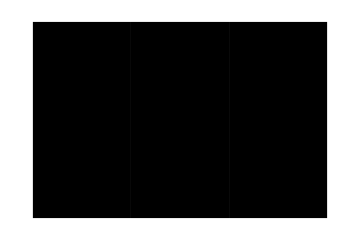
Color Picker
-Graphics-Current Color
-Graphics-

```mathematica
VisualizeColorPickerBox[]
```

```mathematica
VisualizeInput2DCube[]
```

-Graphics-

```mathematica
Button["Validate Cube",Print[ValidateCubeInput[]]]
```

Validate Cube

## I/O cube

### Export

```mathematica
cube3DPieces = GetPieces[Cube2DToString[]];
```

```mathematica
Button["Salva la stringa cubo",Print[Cube3DToString[cube3DPieces]]]
```

Salva la stringa cubo

TTTTWTTTTTTTTTTTTTTTTTRTTBTTOTTGTTTTTTTTTTTTTTTTTYTTTT

#### Import

```mathematica
checkLength[x_]:=If[Length[Characters[x]]==54,Print["La stringa ",x," è un input accettabile."],If[Length[Characters[x]]>54,Print["La stringa ",x," non è un input accettabile (troppo lunga, richiesti 54 caratteri)"],Print["La stringa ",x," non è un input accettabile (troppo corta, richiesti 54 caratteri)"]]];
stringaInput="WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY";
Grid[{{InputField[Dynamic[stringaInput],String,ImageSize->UpTo[1000]],Button["Check",checkLength[stringaInput],ImageSize->UpTo[100]]}}]
```

| Check

La stringa TTTTWTTTTTTTTTTTTTTTTTRTTBTTOTTGTTTTTTTTTTTTTTTTTYTTTT è un input accettabile.

```mathematica
7788
```